{1.}

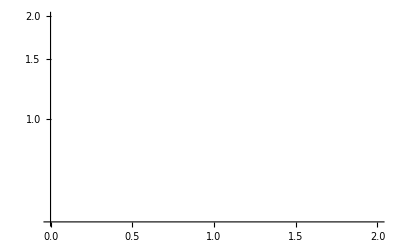

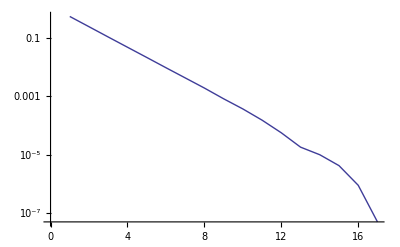

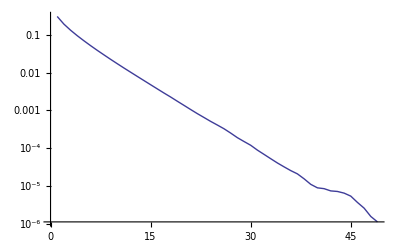

{α→-0.22759,β→-0.229813,γ→-0.744339}

-Graphics3D-

g= 0, acc = 2.05033, ann = 0.637161

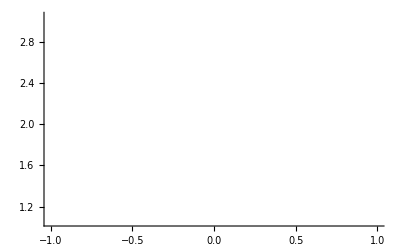

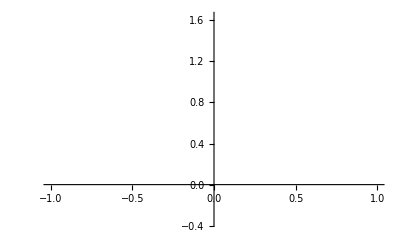

{1.}

{2.3}

{0.8}

{0.0753207,0.0228192,0.22874,9.1149,586.157,47971.,4.52616×10^6}

```mathematica
(* Initialization of coefficients fg,ccg,nng *)
n2ansup[a_]:=Module[{rp,rn,n},
rp=0.0;
rn=3 a;
n=2;
While[rn≥rp,
rp=rn;
rn=((n+1) (n+2))/2 a^n;
n++;
];
rp
];
InitGenusConstants[cc_,NN_,A_,B_,fe_,μ_,ν_,maxg_]:=Module[{fg,ccg,nng,sup,g},
fg=Table[0,{g,1,maxg}];
ccg=Table[0,{g,1,maxg}];
nng=Table[0,{g,1,maxg}];
fg[[1]]=1;ccg[[1]]=cc;nng[[1]]=NN;
For[g=2,g≤maxg,g++,
ccg[[g]]=ccg[[g-1]] (1.0+A/(g-1)^ν);
nng[[g]]=nng[[g-1]] (1.0+B/(g-1)^μ);
 sup=n2ansup[ ccg[[g-1]]/ccg[[g]] ];
fg[[g]]=fe fg[[g-1]]sup;
];
(*(ccg[[g]]^2 nng[[g]])*)
{fg,ccg,nng}
];
(* Importing the actual data *)
FCNData=Transpose[Import["G:\\LAT\\sd_metropolis\\data\\hmm\\fcn_data_l0.0100_nmc20000000.dat","Table"]];
fg=FCNData[[2]];
ccg=FCNData[[3]];
nng=FCNData[[4]];
Print[fg];
GMNHistData=Import["G:\\LAT\\sd_metropolis\\data\\hmm\\gmn_hist_l0.0100_nmc20000000.dat","Table"];
maxg=0; maxt=0; maxn=0;
For[i=1,i≤Length[GMNHistData],i++,
maxg=Max[maxg,GMNHistData[[i,1]]];
maxt=Max[maxt,GMNHistData[[i,2]]];
maxn=Max[maxn,GMNHistData[[i,3]]];
];
maxg++;
maxn=maxn/2;
GMNHist=Table[0,{ig,1,maxg},{it,1,maxt},{in,1,maxn}];
GMNRes=Table[0,{ig,1,maxg},{it,1,maxt},{in,1,maxn}];
GHist=Table[0,{ig,1,maxg}];
THist=Table[0,{it,1,maxt}];
NHist=Table[0,{in,1,maxn}];
For[i=1,i≤Length[GMNHistData],i++,
ig=GMNHistData[[i,1]]+1;
it=GMNHistData[[i,2]];
in=GMNHistData[[i,3]]/2;
GMNHist[[ig,it,in]]=GMNHistData[[i,4]];
GMNRes[[ig,it,in]]=GMNHistData[[i,4]] fg[[ig]] ccg[[ig]]^(2 in) nng[[ig]]^it;
GHist[[ig]]+=GMNHistData[[i,4]];
THist[[it]]+=GMNHistData[[i,4]];
NHist[[in]]+=GMNHistData[[i,4]];
];
(*For[ig=1,ig≤maxg,ig++,
Print[ArrayPlot[GMNHist[[ig]],PlotRange->All,Mesh->False]];
];*)
ListLogPlot[GHist,PlotRange->All,Joined->True]
ListLogPlot[THist,PlotRange->All,Joined->True]
ListLogPlot[NHist,PlotRange->All,Joined->True]
(* Try to estimate the dependence of cc and NN on g *)
accs={}; anns={};
ConFunc[dat_,α_,β_,γ_]:=Module[{Res,i},
Res=True;
For[i=1,i≤Length[dat],i++,
Res=Res && ((α dat[[i,1]] + β dat[[i,2]] + γ)≥dat[[i,3]]);
];
Res
];
For[ig=1,ig≤maxg,ig++,
MNHistToFit={};
For[it=1,it≤maxt,it++,
For[in=1,in≤maxn,in++,
If[GMNHist[[ig,it,in]]>0,AppendTo[MNHistToFit,{it,in,Log[GMNHist[[ig,it,in]]]}]];
];
];
FFF=FindFit[MNHistToFit,{α t + β n + γ,ConFunc[MNHistToFit,α,β,γ]},{α,β,γ},{t,n}];
Print[FFF];
Gr1=ListPointPlot3D[MNHistToFit,PlotRange->All,PlotStyle->{Red}];
Gr2=Plot3D[(α t + β n + γ)/.FFF,{t,1,maxt},{n,1,maxn},Mesh->False];
Print[Show[Gr1,Gr2]];
acc=ccg[[ig]] Exp[β/2]/.FFF; ann = nng[[ig]]Exp[α]/.FFF;
Print["g= ",ig-1,", acc = ",acc, ", ann = ",ann];
AppendTo[accs,{ig-1,acc}];
AppendTo[anns,{ig-1,ann}];
];
ListPlot[accs,Joined->True,PlotRange->All]
ListPlot[anns,Joined->True,PlotRange->All]
(* Now estimate how everything will look like for new values of fgccnn *)
Print[fg];
Print[ccg];
Print[nng];
(* InitGenusConstants[cc_,NN_,A_,B_,fe_,μ_,ν_,maxg_] *)
G4={3.2069970845481026,8.928571428571432,184.5703125000008,26619.58122253439,1.0299475158772552*^7,7.718662398141834*^9,9.511042888107438*^12};
{mfg,mccg, mnng}=InitGenusConstants[2.80,0.8,0.2,0.2,1.4,1.1,1.1,7];
W4=Table[G4[[ig]]/(mfg[[ig]] mccg[[ig]]^4 mnng[[ig]]),{ig,1,Length[mfg]}];
Print[W4];
```

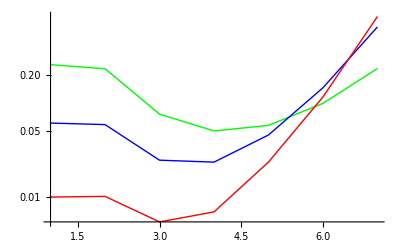

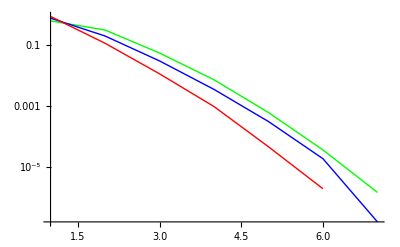

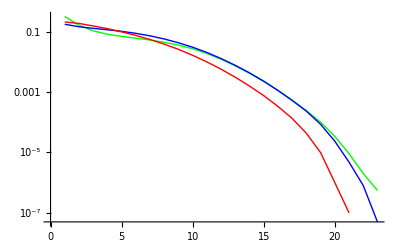

```mathematica
ListLogPlot[{GHist030,GHist035,GHist040},PlotRange->All,Joined->True,PlotStyle->{Green,Blue,Red}]
ListLogPlot[{THist030,THist035,THist040},PlotRange->All,Joined->True,PlotStyle->{Green,Blue,Red}]
ListLogPlot[{NHist030,NHist035,NHist040},PlotRange->All,Joined->True,PlotStyle->{Green,Blue,Red}]
```

```mathematica
G4={2.331961591220858,1.7361111111111145,0.2117156982421859,0.14118687249719838,0.24085526424499215,0.7835580350717017,4.162741334419088};
Manipulate[
{mfg,mccg, mnng}=InitGenusConstants[2.35,0.9,mA,mB,fe,1.1,1.1,7];
(*Print[mccg];*)
W4=Table[G4[[ig]]/(mfg[[ig]] mccg[[ig]]^4 mnng[[ig]]),{ig,1,Length[mfg]}];
GraphicsGrid[{{ListLogPlot[mfg,PlotLabel->"fg"],ListLogPlot[mccg,PlotLabel->"ccg"]},{ListLogPlot[mnng,PlotLabel->"mnng"],ListLogPlot[W4,PlotLabel->"W4"]}}],
{mA,0.015,20.0},{mB,0.005,20.0},{fe,0.1,15.0}
]
```

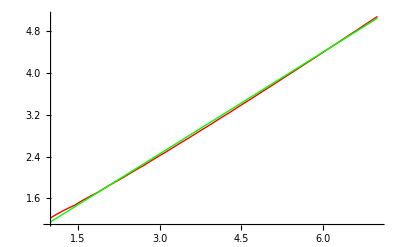

```mathematica
Plot[{√n2ansup[(1.0+1/g^1.1)^-1],0.65 g+0.5},{g,1,7},PlotStyle->{Red,Green}]
```

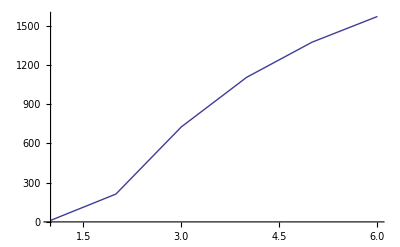

```mathematica
T1=Table[{i,G4[[i+1]]/(i^2 G4[[i]])},{i,1,Length[G4]-1}];
Gr1=ListPlot[T1,Joined->True];
Show[Gr1]
```